Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

Note: Prior to Mathematica 7, GradientFieldPlot was a built-in function, but is now obsolete. In order to use some older plot code, the following module can be incorporated. The module and first image is due to noeckel and is to be seen at https://pages.uoregon.edu/noeckel/computernotes/Mathematica/fieldPlots.html; the second and third images are in MmaSE question 17318, as answered by Jens.

```mathematica
gradientFieldPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=Module[{img,cont,densityOptions,contourOptions,frameOptions,gradField,field,fieldL,plotRangeRule,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[DensityPlot],Except[{Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,Frame->None,Axes->None,AspectRatio->Automatic}];
contourOptions=Join[FilterRules[{opts},FilterRules[Options[ContourPlot],Except[{Prolog,Epilog,FrameTicks,PlotLabel,Background,ContourShading,PlotRangePadding,Frame,Axes,ExclusionsStyle}]]],{PlotRangePadding->None,Frame->None,Axes->None,ContourShading->False}];
gradField=ComplexExpand[{D[f,rx[[1]]],D[f,ry[[1]]]}];
fieldL=DensityPlot[Norm[gradField],rx,ry,Evaluate@Apply[Sequence,densityOptions]];
field=First@Cases[{fieldL},Graphics[__],∞];
img=Rasterize[field,"Image"];
plotRangeRule=FilterRules[Quiet@AbsoluteOptions[field],PlotRange];
cont=If[MemberQ[{0,None},(Contours/.FilterRules[{opts},Contours])],{},ContourPlot[f,rx,ry,Evaluate@Apply[Sequence,contourOptions]]];
frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
If[Head[fieldL]===Legended,Legended[#,fieldL[[2]]],#]&@Apply[Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]}],cont,StreamPlot[gradField,rx,ry,Evaluate@FilterRules[{opts},StreamStyle],Evaluate@FilterRules[{opts},StreamColorFunction],Evaluate@FilterRules[{opts},StreamColorFunctionScaling],Evaluate@FilterRules[{opts},StreamPoints],Evaluate@FilterRules[{opts},StreamScale]],##]&,frameOptions]]
```

The following examples show some plots which are possible with this module.

```mathematica
gfp1=gradientFieldPlot[(y^2+(x-2)^2)^(-1/2)-(y^2+(x-1/2)^2)^(-1/2)/2,{x,-1.5,2.5},{y,-1.5,1.5},PlotPoints->50,ColorFunction->"BlueGreenYellow",Contours->10,ContourStyle->White,Frame->True,FrameLabel->{"x","y"},ClippingStyle->Automatic,Axes->True,StreamStyle->Orange,ImageSize->250];
pot[r_,f_]:=Piecewise[{{-2 e r Cos[f]/(1+er),0≤r<a},{-e r Cos[f]+(er-1)*a^2*e*r^(-1)*Cos[f],r≥a}}](*electorstatic potential*)
e=500;(*outer electric field*)a=0.02;(*cylinder's radius*)er=2;
gfp2=gradientFieldPlot[pot[Sqrt[x^2+y^2],ArcTan[x,y]],{x,-.2,.2},{y,-.2,.2},PlotPoints->50,ColorFunction->"BlueGreenYellow",Contours->10,ContourStyle->White,Frame->True,FrameLabel->{"x","y"},ClippingStyle->Automatic,Axes->True,StreamStyle->Orange,ImageSize->200];
```

```mathematica
gfp3=gradientFieldPlot[pot[Sqrt[x^2+y^2],ArcTan[x,y]],{x,-.05,.05},{y,-.05,.05},PlotPoints->50,ColorFunction->"BlueGreenYellow",Contours->10,ContourStyle->White,Frame->True,FrameLabel->{"x","y"},ClippingStyle->Automatic,Axes->True,StreamStyle->Orange,ImageSize->200];
```

```mathematica
Row[{gfp1,gfp2,gfp3}]
```

-Graphics--Graphics--Graphics-

The following is a useless plot, but maybe I can make use of it later.

```mathematica
gradientFieldPlot[{x,1},{x,-5,5},{y,-5,5},PlotPoints->50,ColorFunction->"BlueGreenYellow",Contours->20,ContourStyle->White,Frame->True,FrameLabel->{"x","y"},ClippingStyle->Automatic,Axes->False,StreamStyle->Orange,ImageSize->200]
```

-Graphics-

1. Differentiability. Under what condition on the velocity vector V in (1) will F[z] be analytic?

The proof of theorem 1 on p. 774 meanders for some time, and in numbered line (8) on p. 774 the assumptions of Green’s theorem are invoked. Referring to the requirements of Green’s, in numbered line (1) on p. 433, the requirement is stated that curves be smooth with continuous partial derivatives.

3. Cylinder. Guess from physics and from fig. 416 where on the y-axis the speed is maximum. Then calculate.

```mathematica
Clear["Global`*"]
```

I have a plot of the function F[z], adapted from from Paul Nylander’s site (http://www.bugman123.com/GANNAA/index.html). The original equation was for z+a^2/z.

```mathematica
U=a=1;w[z_]:=U(z+a/z);
ContourPlot[Im[w[x+I y]],{x,-3,3},{y,-2,2},Contours->Table[psi,{psi,-3,3,0.25}],PlotPoints->100,ContourShading->Automatic,AspectRatio->Automatic,ImageSize->300,Epilog->{Red,Line[{{-3,1},{3,1}}]}]
```

-Graphics-

The flow equation is

```mathematica
F[z]=Φ[x,y] + ⅈ Ψ[x,y]
```

Example 2 gives the equation in polar form

```mathematica
F[z]=r ⅇ^(ⅈ θ)+1/r ⅇ^(-ⅈ θ)
```

But the text answer seems to do it the cartesian way.

```mathematica
F[z_]=z+1/z
```

1/z+z

And a simple derivative, with respect to z, gives the velocity vector.

```mathematica
D[F[z],z]
```

1-1/z^2

The problem asked specifically about the y-axis, so the part of F[z] having to do with y , or Ψ, is inserted.

```mathematica
Abs[F'[ⅈ y]]
```

Abs[1+1/y^2]

The nature of the expression above makes the absolute value sign unnecessary. The radius of the cylinder is a=1, therefore y has to be equal to or larger than this. The answer I am looking for is ‘what value of y gives the maximum velocity and what is that velocity?’

```mathematica
FindMaximum[1+1/y^2&&y≥1,{y}]
```

FindMaximum::nrnum: The function value -False is not a real number at {y} = {0.5}.

{2.,{y→1.}}

The FindMaximum function is not very user friendly. To use it without receiving some kind of warning note is more than I can manage. Incidentally, the red line in the above sketch at y=1, and which is tangent to the cylinder, represents the y-axis position of maximum velocity of the fluid.

5. Irrotational flow. Show that the flow in Example 2 is irrotational.

```mathematica
Clear["Global`*"]
```

Okay, in terms of x and y I have that

```mathematica
F[x_,y_]=(x+ⅈ y)+1/(x+ⅈ y)
```

x+1/(x+ⅈ y)+ⅈ y

and I can take the gradient of it. By numbered line (4) on p. 771 I have that the velocity is the gradient of the Φ function, i.e. V_1=(∂Φ)/(∂x) and V_2=(∂Φ)/(∂y). This is not relevant at the moment, but as for the gradient,

```mathematica
gradxy=Grad[F[x,y],{x,y}]
```

{1-1/(x+ⅈ y)^2,ⅈ-ⅈ/(x+ⅈ y)^2}

I can take the divergence of that

```mathematica
Div[gradxy,{x,y}]
```

0

The green cell above matches the answer in the text and demonstates that F[x,y] =Φ is irrotational.

7. Parallel flow. Sketch and interpret the flow with complex potential F[z]=z.

```mathematica
Clear["Global`*"]
```

The complex potential of a flow regime tells a number of things about it.
F[z]=Φ[x,y] + ⅈ Ψ[x,y]

The real part above gives the velocity potential, and the imaginary part gives the streamlines.
Velocity vectors have both real and imaginary components, and the velocity is computed according to V=V_1 +ⅈ V_2=OverBar[F'[z]] which incorporates the text’s own special vector symbol, which Mathematica can emulate.

Given the complex potential ,

```mathematica
F[z_] = z = x + ⅈ y
```

x+ⅈ y

I can find the derivative with respect to x

```mathematica
D[F[z],x]
```

1

and the velocity vector from the derivative (Mathematica refuses to not dismiss the null imaginary), so I won’t process this line.

```mathematica
D[F[z],x]=1+0 ⅈ
```

and if I wish to, I can look at the components of the velocity vector

```mathematica
V=Subscript[V, 1]=1
```

The positive velocity vector makes it a positive velocity.

```mathematica
Subscript[V, 2]=0
```

I include a sample of two ways to plot the flow, subject to later correction or refinement, and a third visual, which may be loosely related (from MmaSE question 34003, answered by ubpdqn).

```mathematica
p1=ListLinePlot[Table[{x,y},{x,0,10,1},{y,0,10,1}],ImageSize->200,PlotStyle->{{Red,Thickness[0.004]},{Red,Thickness[0.004]}},AxesLabel->{Φ,Ψ},AspectRatio->Automatic];
```

```mathematica
p4=ListLinePlot[Table[Table[{x,y},{x,0,10,1}],{y,0,10,1}],ImageSize->250,PlotStyle->{{Blue,Thickness[0.004]},{Blue,Thickness[0.004]}},AspectRatio->Automatic];
```

```mathematica
p5=ListStreamPlot[Table[{10000,y},{x,-3,3,0.1},{y,-3,3,0.5}],MeshFunctions->Function[{x,y,vx,vy,n},x],Mesh->9,ImageSize->250,FrameLabel->{Φ->equipotential lines,Ψ->streamlines}];
```

```mathematica
μ=0.02;Px=-0.5;h=1.0;
f=(h^2/(2 μ)) (-Px) (1-(y/h)^2)
p6=VectorPlot[{f,0},{x,0,3},{y,-h,h},VectorPoints->Table[{0,j},{j,-1,1,0.1}],VectorScale->{1,0.2},VectorColorFunction->(Hue[#3*.6]&),PlotRange->{{0,4},{-1.1,1.1}},ImageSize->250,Epilog->{{Red,Thick,Line[{{0,1},{4,1}}]},{Red,Thick,Line[{{0,-1},{4,-1}}]}}];
```

12.5 (1-1. y^2)

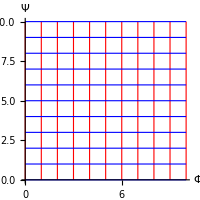
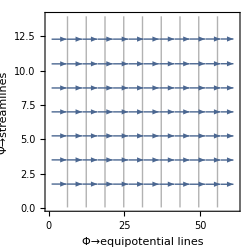
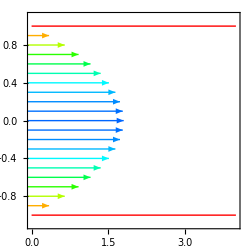

```mathematica
Row[{Show[{p1,p4}],p5,p6}]
```

The following irrelevant plot is one I’m holding onto for the moment.

```mathematica
data=Table[{{x,y},{y,x-x^2}},{x,-1.5,1.5,0.2},{y,-2,2,0.2}];

ListStreamPlot[data,StreamPoints->{{-1.5,1.6},{0.0,0.5},{1.4,0}},Epilog->{PointSize,Red,Point[{{-1.5,1.6},{0.0,0.5},{1.4,0}}]}];
```

9. Corner. What F[z] would be suitable in example 1 if the angle of the corner were π/4 instead of π/2?

```mathematica
Clear["Global`*"]
```

```mathematica
A=.25;beta=4;alpha=2;w[z_]:=A z^alpha;
p1=ContourPlot[Im[w[x+I y]],{x,0,3},{y,0,3},Contours->Table[psi,{psi,0,2.5,0.125}],PlotPoints->100,ContourShading->Automatic,AspectRatio->Automatic,ImageSize->250];
```

```mathematica
A=.25;beta=4;alpha=4;w[z_]:=A z^alpha;
p2=ContourPlot[Im[w[x+I y]],{x,0,3},{y,0,3},Contours->Table[psi,{psi,0,2.5,0.125}],PlotPoints->100,ContourShading->Automatic,AspectRatio->Automatic,ImageSize->250];
```

```mathematica
Row[{p1,p2}]
```

-Graphics--Graphics-

The above plot (at right) suggests that alpha = 4 would be appropriate for a corner with π/4 angle.

11. What flow do you obtain from F[z] = -ⅈ K z, K positive real?

```mathematica
Clear["Global`*"]
```

Starting with F[z]=Φ[x,y] + ⅈ Ψ[x,y], F[z] = ⅈ K z means that there is no Φ function, so no flow in the horizontal direction, and that there are no equipotential lines. There can still be vertical flow though, with source at the origin.

```mathematica
F[z_] = ⅈ K z
```

ⅈ K z

Since according to numbered line (3) on p. 771, OverBar[F'[z]] is the velocity vector equal to V_1+ⅈ V_2

```mathematica
D[F[z],z]
```

ⅈ K

then OverBar[F'[z]]=ⅈ K, so that V_1=0 and V_2=K.

13. 60°-Sector. What F[z] would be suitable in example 1 if the angle at the corner were π/3?

```mathematica
Clear["Global`*"]
```

Based on what was done with corners before, an intuitive approach seems justified.

```mathematica
A=.25;beta=4;alpha=3;w[z_]:=A z^alpha;
p2=ContourPlot[Im[w[x+I y]],{x,0,3},{y,0,3},Contours->Table[psi,{psi,0,2.5,0.125}],PlotPoints->100,ContourShading->Automatic,AspectRatio->Automatic,ImageSize->250]
```

-Graphics-

It seems that alpha=3 would give the best plot for a case of a (π/3)-angled corner.

15. Change F[z] in example 2 slightly to obtain a flow around a cylinder of radius r_0 that gives the flow in example 2 if r_0 ⟶1.

```mathematica
Clear["Global`*"]
```

From the red line in the figure it can be seen that the cylinder radius is already 1. And the problem doesn’t want to change the velocity, it just wants to keep it as what has already been calculated. So the problem is really just asking for an alternate expression of the formula.

```mathematica
U=a=1;w[z_]:=U(z+a/z);
ContourPlot[Im[w[x+I y]],{x,-3,3},{y,-2,2},Contours->Table[psi,{psi,-3,3,0.25}],PlotPoints->100,ContourShading->Automatic,AspectRatio->Automatic,ImageSize->300,Epilog->{Red,Line[{{-3,1},{3,1}}]}]
```

-Graphics-

I already know that
F[z] = [r,θ] +ⅈ Ψ[r,θ]
and with piercing insight of U, I can write this as equal to
a z + 1/(a z) 
and going polar I can express the last as
a r ⅇ^(ⅈ θ) + 1/(a r)ⅇ^(-ⅈ θ)

The main topic being streamlines, I can concentrate on Ψ, the imaginary part of F, and write

```mathematica
FullSimplify[ExpToTrig[Im[a r ⅇ^(ⅈ θ) + 1/(a r)ⅇ^(-ⅈ θ)]]]
```

Im[(1/(a r)+a r) Cos[θ]]+Re[(-1/(a r)+a r) Sin[θ]]

Of the two terms above, the imaginary one has no imaginary components, so I drop it, which leaves

```mathematica
(-1/(a r)+a r) Sin[θ]
```

The streamlines in the figure do not have constant Arg, but at a given point they do.  For example, the red line, tangent to the cylinder, is like a derivative to that streamline hugging the cylinder most closely. The Arg is constant. Thus I could say

```mathematica
(-1/(a r)+a r)=const
```

And even further, since there is no sine quantity, I could say

```mathematica
(-1/(a r)+a r)=0
```

And I can solve for the variable a

```mathematica
Solve[-1/(a r)+a r==0,a]
```

{{a→-1/r},{a→1/r}}

I choose the simpler solution for a and recapitulate

F[z] = a z + 1/(a z) = z/r + r/z

It is interesting that the problem expression generalizes into such a simple formula.

17. Elliptic cylinder. Show that F[z] = ArcCos[z] gives confocal ellipses as streamlines, with foci at z = ±1, and that the flow circulates around an elliptic cylinder or a plate (the segment from -1 to 1 in the figure below).

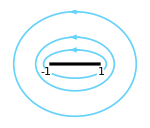

```mathematica
kru=RGBColor[0.392,0.823,0.98];
Graphics[{{kru,Thickness[0.008],Circle[{0,0},{1.17,1},{0,2π}]},{kru,Thickness[0.008],Circle[{0,0},{0.75,0.5128},{0,2π}]},{kru,Thickness[0.008],Circle[{0,0},{0.6,0.27},{-0.4,π+0.3}]},{kru,Thickness[0.008],Circle[{0,0},{0.6,0.27},{-2.4,-0.8}]},{kru,Arrowheads[.07],Arrow[{{0.1,0.5128},{-0.1,0.5128}}]},{kru,Arrowheads[.07],Arrow[{{0.1,0.27},{-0.1,0.27}}]},{kru,Arrowheads[.07],Arrow[{{0.1,1},{-0.1,1}}]},{Rectangle[{-0.49,-0.03},{0.49,0.03}]},{Text[Style["-1",Medium],{-0.55,-0.15}]},{Text[Style["1",Medium],{0.5,-0.15}]}},Axes->False,ImageSize->150]
```

```mathematica
Clear["Global`*"]
```

F[z] = ArcCos[z] looks like a flow formula with a Φ part but no Ψ part. At first glance it would seem to be without streamlines.

```mathematica
F[z_]=ArcCos[z]
```

ArcCos[z]

```mathematica
D[F[z],z]
```

-1/(√(1-z^2))

describes the velocity vector. So it might be that V_1= -1/(√(1-z^2)), V_2 = 0 . If the flow has velocity, I guess it has circulation. If the positive value of V_1 in problem 7 indicated a velocity directed to the right, maybe the minus sign of V_1 here indicates circulation to the left to match the figure above. The velocity in a vertical direction seems to be null. However, there is no restriction on the composition of z, and maybe it contains within it the circularity of circulation which is suggested by the figure.

```mathematica
U=a=1;w[z_]:=U(ArcCos[z]);
p1=ContourPlot[Im[w[x+I y]],{x,-3,3},{y,-3,3},Contours->Table[psi,{psi,-3,3,0.25}],PlotPoints->100,ContourShading->Automatic,AspectRatio->Automatic,ImageSize->300,Axes->True,Epilog->{{White,PointSize[0.001],Point[{0,0.8225}]},{Black,PointSize[0.001],Point[{1.295,0}]},{White,PointSize[0.001],Point[{0,2.1269}]},{Black,PointSize[0.001],Point[{2.3505,0}]}}];
```

```mathematica
p2=ContourPlot[{(x/1.295)^2+(y/0.8225)^2==1,(x/2.3505)^2+(y/2.1269)^2==1},{x,-3,3},{y,-3,3},AspectRatio->Automatic, ImageSize->300,ContourStyle->{{White,Thickness[0.004]},{White,Thickness[0.004]}}];
```

```mathematica
Row[{p1,Show[{p1,p2}]}]
```

-Graphics--Graphics-

The ContourPlot is written to show only the imaginary, so what it shows, I suppose, must be streamlines. The first plot above shows the minor axis point locations, as well as major, which, however, are harder to see without zoom. On my monitor, on the second plot, the white ellipses mask black, showing good approximation for the ellipse equations.

For the larger ellipse the focus is at (plus or minus)

```mathematica
√((2.3505)^2-(2.1269)^2)
```

1.00057

And for the smaller ellipse the focus is at (plus or minus)

```mathematica
√((1.295)^2-(0.8225)^2)
```

1.00026

The focus results argue (visually) for confocality.

19. Potential F[z] = 1/z. Show that the streamlines of F[z] = 1/z and circles through the origin with centers on the y-axis.

```mathematica
Clear["Global`*"]
```

```mathematica
U=a=1;w[z_]:=U(1/z);
p1=ContourPlot[Im[w[x+I y]],{x,-3,3},{y,-3,3},Contours->Table[psi,{psi,-3,3,0.25}],PlotPoints->100,ContourShading->Automatic,AspectRatio->Automatic,ImageSize->300,Axes->True];
```

```mathematica
p2=ContourPlot[Im[w[x+I y]],{x,-0.1,0.1},{y,-0.1,0.1},Contours->3,PlotPoints->100,ContourShading->None,AspectRatio->Automatic,ImageSize->300,Axes->True];
```

The left plot shows circles on the y-axis (visual judgment), and origin point shared by circles’ curves (also visual). A zoomed version is at right.

```mathematica
Row[{p1,p2}]
```

-Graphics--Graphics-